# Net Sport Model

## Utilities

```mathematica
lightBeige = RGBColor[1.,0.9920042725261311,0.8800030518043793];
```

```mathematica
SetOptions[EvaluationNotebook[],Background-> lightBeige]
```

```mathematica
ClearAll["Global`*"]
```

## Functions

### Initialization

```mathematica
initgame[width_]:= Module[{court, net, abline, hbline, astart, dstart, bstart, framerate,startpos }, 
court = Rectangle[{1, 1} - playerSize, {width, courtLength}+playerSize]; 
net = Line[{{1, (courtLength+1)/2 }, {width, (courtLength + 1) / 2}}];
abline = Subdivide[{1, courtLength}, {width, courtLength}, width -1 ];
hbline =Subdivide[{1, 1}, {width, 1}, width -1 ];
astart = First[hbline];
dstart  = First[abline];
bstart = astart;
framerate = 12;
startpos = <|"hpos"->astart, "apos"->dstart,"bpos"->bstart|>
]
```

### Helper

```mathematica
getdist[start_, dest_]:= EuclideanDistance[start, dest]
```

```mathematica
restrict[val_, {min_, max_}]:= If[val < min, min, If[val>max,max, val]];
```

```mathematica
gettime[start_, dest_, speed_, rtime_:0]:= Floor[EuclideanDistance[start, dest] / speed] - rtime;
```

```mathematica
getinfo[pos_, params_]:= Module[{homeQ, homeaway, attdef, attdefstring, blines},
homeQ= pos["bpos"][[2]] == params["hbline"][[1, 2]];
homeaway = {pos["hpos"], pos["apos"]};
attdef = If[homeQ, homeaway, Reverse@homeaway ];
attdefstring = If[homeQ, {"hpos", "apos"}, {"apos", "hpos"}];
blines = If[homeQ, {params["hbline"], params["abline"]},  Reverse@{params["hbline"], params["abline"]}];
<|"homeQ"->homeQ, 
"att"->attdef[[1]],
"def"->attdef[[2]],
"attstring"-> attdefstring[[1]],
"defstring"->attdefstring[[2]], 
"attbline"->blines[[1]],
"defbline"->blines[[2]]
|>
]
```

### Visualization

```mathematica
getPoint[center_,angle_,radius_]:=center+radius*AngleVector[angle]
```

```mathematica
getRecPoints[point_, size_]:={getPoint[point, 225Degree, size], getPoint[point, 45Degree, size]}
```

```mathematica
getTriPoints[point_, size_]:=
{getPoint[point, 88Degree, size - 1/12],getPoint[point, 210 Degree, size], getPoint[point, 330Degree, size ]}
```

```mathematica
getObjectShapes[pos_]:= 
{Rectangle@@getRecPoints[pos["hpos"], playerSize], N@Polygon@getTriPoints[pos["apos"],playerSize], 
Disk[pos["bpos"], ballSize]}
```

```mathematica
Options[show] = {"points"->{}};
show[pos_Association, OptionsPattern[{show, Graphics}]]:= Module[{hrec, atri, ball}, 
{hrec, atri, ball} = getObjectShapes[pos];
Graphics[{FaceForm@White, EdgeForm@Black,court,singleslines, net,EdgeForm@None, FaceForm@Gray, Point@N@OptionValue["points"], FaceForm@Blue, hrec,FaceForm@Red,atri, Green, ball},ImageSize->OptionValue[ImageSize]]
]
```

```mathematica
show[poss_List]:= ListAnimate[show/@ poss, DefaultDuration->Length@poss/65, AnimationRepetitions->1]
```

```mathematica
animateobj[start_, dest_List, speed_, reactiontime_:0, timespec_:-1]:=Module[{ptime, movetime, move, react, wtime, wait},
ptime = Max[gettime[start, dest, speed], 1];
movetime = If[timespec == -1, ptime+reactiontime, timespec];
move = Subdivide[start, dest, ptime*framerate];
react = Join[Table[start, reactiontime*framerate],move];
wtime =movetime*framerate;
wait = PadRight[react, wtime, {Last@react}]
]
```

```mathematica
animateshot[{pos1_, pos2_},params_]:= Module[{i1, i2, timespec, att, def, amove, dmove, bmove},
i1 = getinfo[pos1, params];
i2 = getinfo[pos2, params]; 
timespec = gettime[pos1["bpos"], pos2["bpos"], params["shotspeed"]];
att = pos1[i1["attstring"]];
def = pos1[i1["defstring"]];
amove = animateobj[i1["att"], i2["def"],params["pspeed"], swingtime, timespec];
dmove = animateobj[i1["def"], i2["att"], params["pspeed"], params["rtime"], timespec];
bmove =  animateobj[pos1["bpos"],pos2["bpos"], params["shotspeed"], 0, timespec];
MapThread[<|i1["attstring"]->#1, i1["defstring"]->#2, "bpos"->#3|>&, {amove, dmove, bmove}]
]
```

```mathematica
animatepoint[poslist_]:=Module[{pairs}, 
 pairs = Partition[poslist, 2, 1];
Flatten[animateshot[#, params]&/@ pairs, 1]
]
```

### Evaluation

```mathematica
winnerQ[pos_, dest_,info_, params_]:= Module[{ddist, bdist, dtime, btime},
ddist = EuclideanDistance[dest,info["def"]];
bdist =  EuclideanDistance[dest,pos["bpos"]];
dtime =  ddist+params["rtime"]/params["pspeed"];
btime = bdist / params["shotspeed"];
btime < dtime
]
```

```mathematica
getwinnerease[params_]:= Module[{dests},
dests = Table[{i, courtLength}, {i, params["cwidth"]}];
Count[winnerQ[initgame[params["cwidth"]], #, params]&/@dests, True]
]
```

```mathematica
getwinnercount[pos_, params_]:= Module[{info, shots, qs}, 
info = getinfo[pos, params];
shots = info["defbline"];
qs =winnerQ[pos, #,info, params]&/@shots;
Count[qs, True]
]
```

```mathematica
result[pos_, params_]:=Module[{linestring,win, def, team,  line, in, ball},
ball = pos["bpos"];
{linestring, win, def} = If[ball[[2]]== params["hbline"][[1, 2]],{"hbline", 1, pos["hpos"]},  {"abline", 1, pos["apos"]}];
line =  params[linestring];
in = params[linestring<>"in"];
Which[
MemberQ[in, ball] && ball!= def, win, 
!MemberQ[in, ball], -win,
True, 0
]]
```

### Game Logic

```mathematica
movedefender[pos_,info_, params_, bdest_ ]:= Module[{bdist,pdisp, dir, time, disp, moveX},
bdist = EuclideanDistance[bdest, pos["bpos"]];
pdisp = First@bdest- First@info["def"];
dir = Sign[pdisp];
time = Floor[bdist / params["shotspeed"]] - params["rtime"];
disp = dir*(Min[Floor[params["pspeed"]*time], Abs@pdisp]);
moveX =restrict[First@info["def"]+disp, {First@First@params["ablinein"], First@Last@params["ablinein"]}];
{moveX, info["def"][[2]]}
]
```

```mathematica
aimshot[pos_,info_, params_]:= Module[{linein, agg, acc, sideX, shots, shotsX},
linein = If[pos["bpos"][[2]] ==  params["hbline"][[1, 2]],params["ablinein"], params["hblinein"]];
agg = params["aggression"];
acc = params["accuracy"];
sideX =RandomChoice@{First@linein[[1]]+agg, First@linein[[-1]] - agg} ;
shotsX = Range[Max[sideX - acc, 1], Min[sideX + acc, params["cwidth"]], 1];
shots = {#, linein[[1, 2]]}&/@ shotsX;
shots
]
```

```mathematica
recover[pos_,info_, params_, dest_]:= Module[{shottime, recdist,moveXs, moves,moveposlist, bestpos},
shottime = gettime[pos["bpos"], dest, params["shotspeed"], swingtime];
recdist = shottime*params["pspeed"];
moveXs = Range[Max[First@info["att"] - recdist, 1], Min[First@info["att"] + recdist, params["cwidth"]], 1];
moves = Thread[{#, info["att"][[2]]}&[moveXs]];
moveposlist =<|info["attstring"]->#,"bpos"->dest, info["defstring"]->dest|>&/@moves;
wcs =  getwinnercount[#, params]&/@ moveposlist;
(*Echo@wcs;*)
bestpos = First@MinimalBy[moveposlist, getwinnercount[#, params]&,  1];
bestpos[info["attstring"]]
]
```

```mathematica
hit[pos_, params_]:= Module[{info,shots,  dest, newd, recatt},
info = getinfo[pos, params];
shots =aimshot[pos,info, params] ;
dest = RandomChoice@shots;
(*Echo@winnerQ[pos, dest, info, params];*)
newd = movedefender[pos,info, params,dest];
recatt = recover[pos, info, params, dest];
<|info["attstring"]->recatt, info["defstring"]->newd, "bpos"->dest|>
]
```

```mathematica
playpoint[pos_, params_, max_:5]:= NestWhileList[hit[#,params]&,pos, result[#, params]== 0&,1, max]
```

```mathematica
ClearAll@recover
```

### Development

## Running Code

### Gameplay

```mathematica
Column[p = playpoint[startpos, params, 10]];
```

```mathematica
ap = animatepoint[p];
```

```mathematica
show@ap
```

### Saving Data

```mathematica
Length@ap
```

64

```mathematica
gframes = show/@ ap;
```

```mathematica
gframespad = PadRight[gframes, Length@gframes+10, Last@gframes];
```

```mathematica
Export["Projects/Wolfram/SummerSchool/NetSportModel/rally4.gif", gframespad, OverwriteTarget->False]
```

Projects/Wolfram/SummerSchool/NetSportModel/rally4.gif

### Constants

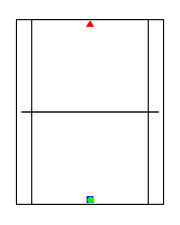

```mathematica
courtLength = 24;
courtWidth  =19;
out = 2;
playerSize = 12/courtWidth;
ballSize = 8/courtWidth;
court = Rectangle[{1, 1} - playerSize, {courtWidth, courtLength}+playerSize]; 
singleslines = Rectangle[{1+out, 1} - playerSize, {courtWidth-out, courtLength}+playerSize]; 
net = Line[{{1, (courtLength+1)/2 }, {courtWidth, (courtLength + 1) / 2}}];
abline = Subdivide[{1, courtLength}, {courtWidth, courtLength}, courtWidth -1 ];
hbline =Subdivide[{1, 1}, {courtWidth, 1}, courtWidth -1 ];
hblinein = ArrayPad[hbline, {-out}];
ablinein = ArrayPad[abline, {-out}];
astart = Median[hbline];
dstart  = Median[abline];
bstart = astart;
framerate = 4;
startpos = <|"hpos"->astart, "apos"->dstart,"bpos"->bstart|>;
info = getinfo[startpos];
show[startpos, ImageSize->Small]
swingtime = 1;
```

### Parameters

```mathematica
params = <|
"cwidth"->  courtWidth,
"abline"->abline,
"hbline"->hbline,
"ablinein"->ablinein,
"hblinein"->hblinein,
"shotspeed"->  4,
"pspeed"->  1,
"rtime"->  0,
"accuracy"->2,
"aggression" ->2
|>;
```

## Analysis

```mathematica
getwinnerease[params]
```

2

### Shot Speed

```mathematica
tps = <|"cwidth"->  5,"shotspeed"->  ss,"pspeed"->  1,"rtime"->  1|>;
```

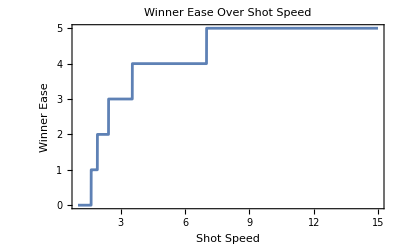

```mathematica
Plot[getwinnerease[tps], {ss, 1, 15}, PlotHighlighting->None,Frame->{True, True, False, False},FrameLabel->{"Shot Speed", "Winner Ease"}, PlotLabel->"Winner Ease Over Shot Speed", PlotRange->All]
```

### Shot Speed With Court Width

```mathematica
tpsList =<|"cwidth"->  #,"shotspeed"->  ss,"pspeed"->  1,"rtime"->  1|>&/@ Range[5, 10];
```

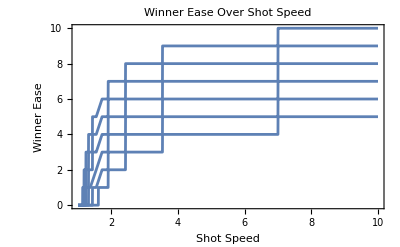

```mathematica
Plot[getwinnerease/@ tpsList, {ss, 1, 10}, PlotHighlighting->None,Frame->{True, True, False, False},FrameLabel->{"Shot Speed", "Winner Ease"}, PlotLabel->"Winner Ease Over Shot Speed", PlotRange->All]
```

### Reaction Time

```mathematica
tps = <|"cwidth"->  10,"shotspeed"->  2,"pspeed"->  1,"rtime"->  rt|>;
```

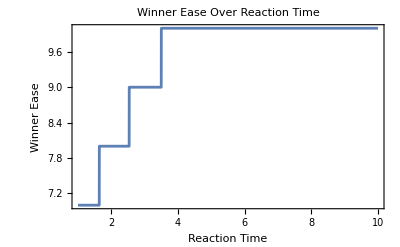

```mathematica
Plot[getwinnerease[tps], {rt, 1, 10}, PlotHighlighting->None,Frame->{True, True, False, False},FrameLabel->{"Reaction Time", "Winner Ease"}, PlotLabel->"Winner Ease Over Reaction Time", PlotRange->All]
```